```mathematica
f[c_][z_]:=z^2+c
k[n_][c_]:=Nest[f[c],c,n]
```

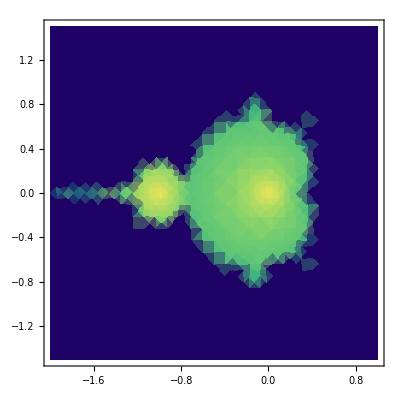

```mathematica
h[x_,y_]:=1/(1+Abs[k[45][x+I*y]]);
DensityPlot[h[x,y],{x,-2,1},{y,-1.5,1.5},ColorFunction->"BlueGreenYellow"]
```